```mathematica
rules ={
Subscript[C, α1]->80000.0,Subscript[C, α2]->80000.0,Subscript[C, α3]->80000.0,Subscript[C, α4]->80000.0,
Subscript[μ, 1]->1.0,Subscript[μ, 2]->1.0,Subscript[μ, 3]->1.0,Subscript[μ, 4]->1.0,
Subscript[F, z1]->26719.0,Subscript[F, z2]->26719.0,Subscript[F, z3]->21295.0,Subscript[F, z4]->21295.0(*NOT SURE*),
m ->2050.0,Subscript[ω, t]->1.63,Subscript[l, f]->1.43,Subscript[l, r]->1.47 , Subscript[J, z] -> 3344.0 ,
Subscript[K, y]-> -0.1,Subscript[K, ψ]-> -1.1,Subscript[ψ, d1] ->0.1

};

τ0 -> {0,10,20,30};
τ -> {5,5,5,5};
Subscript[β, r]-> {0.1,0.5,-0.5,-0.1};

Brake1[t_,τ_,βr_]:=βr*((1+Tanh[20t])/2-(1+Tanh[20(t-τ)])/2);
Brake2[t_,τ0_,τ_,βr_]:= Fold[Plus,0,Table[Brake1[t-τ0⟦k⟧,τ⟦k⟧,βr⟦k⟧],{k,1,Length[τ]}]];
Ratio1[βr_]:= ( Sqrt[1.0-βr^2]);

η -> Ratio1[(Brake2[t,τ0 ,τ ,Subscript[β, r]])];

vRules2={Subscript[ψ, d]->Function[t,$dumy]/.$dumy->(0.1Sin[10 t]/.rules)};
vRules={δ->(Subscript[K, y] Subscript[e, y][t]+Subscript[K, ψ] Subscript[e, ψ][t]+Subscript[K, ψ] Subscript[ψ, d][t]-Subscript[K, ψ] Subscript[ψ, d1]/.vRules2/.rules)};


Slip angle;
Subscript[α, sl1]=ArcTan[3η*Subscript[μ, 1] Subscript[F, z1]/Subscript[C, α1]]/.rules;
Subscript[α, sl2]=ArcTan[3η*Subscript[μ, 2] Subscript[F, z2]/Subscript[C, α2]]/.rules;
Subscript[α, sl3]=ArcTan[3η*Subscript[μ, 3] Subscript[F, z3]/Subscript[C, α3]]/.rules;
Subscript[α, sl4]=ArcTan[3η*Subscript[μ, 4] Subscript[F, z4]/Subscript[C, α4]]/.rules;

Subscript[α, 1]=((y'[t] + Subscript[l, f] ψ'[t])/x'[t])-δ/.vRules/.rules;
Subscript[α, 2]=((y'[t] + Subscript[l, f] ψ'[t])/x'[t])-δ/.vRules/.rules;
Subscript[α, 3]=((y'[t] + Subscript[l, f] ψ'[t])/x'[t])-0/.rules;
Subscript[α, 4]=((y'[t] + Subscript[l, f] ψ'[t])/x'[t])-0/.rules;

Tire Lateral Force;

Subscript[f, x1]=(Brake2[t,τ0,τ,Subscript[β, r]])*Subscript[μ, 1] Subscript[F, z1]/.rules;
Subscript[f, x2]=(Brake2[t,τ0,τ,Subscript[β, r]])*Subscript[μ, 2] Subscript[F, z2]/.rules;
Subscript[f, x3]=(Brake2[t,τ0,τ,Subscript[β, r]])*Subscript[μ, 3] Subscript[F, z3]/.rules;
Subscript[f, x4]=(Brake2[t,τ0,τ,Subscript[β, r]])*Subscript[μ, 4] Subscript[F, z4]/.rules;

Tire Longitudnal Force;

Subscript[Term, 1] = -Subscript[C, α1]Tan[Subscript[α, 1]]+ ((Subscript[C, α1])^2/(3η*Subscript[μ, 1] Subscript[F, z1]) Abs[Tan[Subscript[α, 1]]] Tan[Subscript[α, 1]])- ((Subscript[C, α1])^3/(27((η)^2 Subscript[μ, 1] Subscript[F, z1])^2)(Tan[Subscript[α, 1]])^3)/.rules;
Subscript[Term, 12] = -η Subscript[μ, 1] Subscript[F, z1] Sign[Subscript[α, 1]]/.rules;

Subscript[Term, 2] = -Subscript[C, α2] Tan[Subscript[α, 2]]+ ((Subscript[C, α2])^2/(3η*Subscript[μ, 2] Subscript[F, z2]) Abs[Tan[Subscript[α, 2]]] Tan[Subscript[α, 2]])- ((Subscript[C, α2])^3/(27(η^2 Subscript[μ, 2] Subscript[F, z2])^2)(Tan[Subscript[α, 2]])^3)/.rules;
Subscript[Term, 22] = -η Subscript[μ, 2] Subscript[F, z2] Sign[Subscript[α, 2]]/.rules;

Subscript[Term, 3] = -Subscript[C, α3] Tan[Subscript[α, 3]]+ ((Subscript[C, α3])^2/(3η*Subscript[μ, 3] Subscript[F, z3]) Abs[Tan[Subscript[α, 3]]] Tan[Subscript[α, 3]])- ((Subscript[C, α3])^3/(27(η^2 Subscript[μ, 3] Subscript[F, z3])^2)(Tan[Subscript[α, 3]])^3)/.rules;
Subscript[Term, 32] = -η Subscript[μ, 3] Subscript[F, z3] Sign[Subscript[α, 3]]/.rules;

Subscript[Term, 4] = -Subscript[C, α4] Tan[Subscript[α, 4]]+ ((Subscript[C, α4])^2/(3η*Subscript[μ, 4] Subscript[F, z4]) Abs[Tan[Subscript[α, 4]]] Tan[Subscript[α, 4]])- ((Subscript[C, α4])^3/(27(η^2 Subscript[μ, 4] Subscript[F, z4])^2)(Tan[Subscript[α, 4]])^3)/.rules;
Subscript[Term, 42] = -η Subscript[μ, 4] Subscript[F, z4] Sign[Subscript[α, 4]]/.rules;

Subscript[f, y1]=Piecewise[{{Subscript[Term, 1],(Abs[Subscript[α, 1]])<Subscript[α, sl1]},{Subscript[Term, 12],(Abs[Subscript[α, 1]])≥Subscript[α, sl1]}}]/.rules;
Subscript[f, y2]=Piecewise[{{Subscript[Term, 2],(Abs[Subscript[α, 2]])<Subscript[α, sl2]},{Subscript[Term, 22],(Abs[Subscript[α, 2]])≥Subscript[α, sl2]}}]/.rules;
Subscript[f, y3]=Piecewise[{{Subscript[Term, 3],(Abs[Subscript[α, 3]])<Subscript[α, sl3]},{Subscript[Term, 32],(Abs[Subscript[α, 3]])≥Subscript[α, sl3]}}]/.rules;
Subscript[f, y4]=Piecewise[{{Subscript[Term, 4],(Abs[Subscript[α, 4]])<Subscript[α, sl4]},{Subscript[Term, 42],(Abs[Subscript[α, 4]])≥Subscript[α, sl4]}}]/.rules;

Subscript[F, x1] = Subscript[f, x1] Cos[δ] - Subscript[f, y1] Sin[δ]/.vRules/.rules;
Subscript[F, x2] = Subscript[f, x2] Cos[δ] - Subscript[f, y2] Sin[δ]/.vRules/.rules;
Subscript[F, x3] = Subscript[f, x3] Cos[0] - Subscript[f, y3] Sin[0]/.rules;
Subscript[F, x4] = Subscript[f, x4] Cos[0] - Subscript[f, y4] Sin[0]/.rules;

Subscript[F, y1] = Subscript[f, x1] Sin[δ] + Subscript[f, y1] Cos[δ]/.vRules/.rules;
Subscript[F, y2] = Subscript[f, x2] Sin[δ] + Subscript[f, y2] Cos[δ]/.vRules/.rules;
Subscript[F, y3] = Subscript[f, x3] Sin[0] + Subscript[f, y3] Cos[0]/.rules;
Subscript[F, y4] = Subscript[f, x4] Sin[0] + Subscript[f, y4] Cos[0]/.rules;

Eq1 = m D[x[t],{t,2}] == m D[y[t],{t,1}]D[ψ[t],{t,1}] + Subscript[F, x1] +Subscript[F, x2] +Subscript[F, x3] +Subscript[F, x4]/.rules;
Eq2 = m D[y[t],{t,2}] == -m D[x[t],{t,1}] D[ψ[t],{t,1}] + Subscript[F, y1]+ Subscript[F, y2]+ Subscript[F, y3]+ Subscript[F, y4]/.rules;
Eq3 =Subscript[J, z] D[ψ[t],{t,2}] == Subscript[l, f](Subscript[F, y1] + Subscript[F, y2]) - Subscript[l, r]*(Subscript[F, y3] + Subscript[F, y4]) + (Subscript[ω, t]/2)(-Subscript[F, x1] + Subscript[F, x2] - Subscript[F, x3] + Subscript[F, x4])/.rules;
Eq4 = m D[Subscript[e, ψ][t],{t,1}]==m D[ψ[t],{t,1}]-m D[Subscript[ψ, d][t],{t,1}]/.vRules2/.rules;
Eq5 = m D[Subscript[e, y][t],{t,1}]==m D[y[t],{t,1}] Cos[Subscript[e, ψ][t]] + m D[x[t],{t,1}]Sin[Subscript[e, ψ][t]]/.rules;

time = 25;

solution=NDSolve[{Eq1,Eq2,Eq3,Eq4,Eq5,x[0]==0.1,x'[0]==0.1,y[0]==0.1,y'[0]==0.01,ψ[0]==0.01,ψ'[0]==0.01,Subscript[e, y][0]==0.08,Subscript[e, ψ][0]==0.1},{x,y,ψ,Subscript[e, y],Subscript[e, ψ]},{t,0,time}]

Plot[Evaluate[{x[t],y[t]}/.solution],{t,0,time},Frame->True,FrameLabel->{"t","x,y"},PlotLegends->{"x(t)","y(t)"},PlotRange->All] 
Plot[Evaluate[{x'[t],y'[t]}/.solution],{t,0,time},Frame->True,FrameLabel->{"t","vx,vy"},PlotLegends->{"vx(t)","vy(t)"},PlotRange->All] 
Plot[Evaluate[{x''[t],y''[t]}/.solution],{t,0,time},Frame->True,FrameLabel->{"t","ax,ay"},PlotLegends->{"ax(t)","ay(t)"},PlotRange->All] 
Plot[Evaluate[{η}/.solution],{t,0,time},Frame->True,FrameLabel->{"t","η"},PlotLegends->{"η"},PlotRange->All] 
Plot[Evaluate[{δ/.vRules}/.solution],{t,0,time},Frame->True,FrameLabel->{"t","δ"},PlotLegends->{"δ"},PlotRange->All]
ParametricPlot[Evaluate[{x[t],y[t]}/.solution],{t,0,time},PlotRange-> All]
```

NDSolve::ndinid: Initial condition Sign[0.251  - 1.\ ArcTan[1.00196\ η]] is not in the range specified by the discrete variable NDSolve`s$105335.

NDSolve::ndinid: Initial condition Sign[0.243  - 1.\ ArcTan[0.798563\ η]] is not in the range specified by the discrete variable NDSolve`s$105766.

NDSolve[{2050. x''[t]==-2 (Piecewise[{{80000. Tan[0.11-0.11 Sin[10 t]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]-1/η 79843.3 Abs[Tan[0.11-0.11 Sin[10 t]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[0.11-0.11 Sin[10 t]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]+1/η^4 26562.3 Tan[0.11-0.11 Sin[10 t]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]^3, Abs[-0.11+0.11 Sin[10 t]+0.1 e_y[t]+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]<ArcTan[1.00196 η]}, {-26719. η Sign[-0.11+0.11 Sin[10 t]+0.1 e_y[t]+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]], Abs[-0.11+0.11 Sin[10 t]+0.1 e_y[t]+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]≥ArcTan[1.00196 η]}, {0, True}}]) Sin[0.11-0.11 Sin[10 t]-0.1 e_y[t]-1.1 e_ψ[t]]+2050. y'[t] ψ'[t],2050. y''[t]==2 (Piecewise[{{-80000. Tan[(y'[t]+1.43 ψ'[t])/x'[t]]+(100180. Abs[Tan[(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[(y'[t]+1.43 ψ'[t])/x'[t]])/η-(41816.8 Tan[(y'[t]+1.43 ψ'[t])/x'[t]]^3)/η^4, Abs[(y'[t]+1.43 ψ'[t])/x'[t]]<ArcTan[0.798563 η]}, {-(21295. η Sign[y'[t]+1.43 ψ'[t]])/Sign[x'[t]], Abs[(y'[t]+1.43 ψ'[t])/x'[t]]≥ArcTan[0.798563 η]}, {0, True}}])+2 Cos[0.11-0.11 Sin[10 t]-0.1 e_y[t]-1.1 e_ψ[t]] (Piecewise[{{80000. Tan[0.11-0.11 Sin[10 t]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]-1/η 79843.3 Abs[Tan[0.11-0.11 Sin[10 t]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[0.11-0.11 Sin[10 t]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]+1/η^4 26562.3 Tan[0.11-0.11 Sin[10 t]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]^3, Abs[-0.11+0.11 Sin[10 t]+0.1 e_y[t]+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]<ArcTan[1.00196 η]}, {-26719. η Sign[-0.11+0.11 Sin[10 t]+0.1 e_y[t]+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]], Abs[-0.11+0.11 Sin[10 t]+0.1 e_y[t]+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]≥ArcTan[1.00196 η]}, {0, True}}])-2050. x'[t] ψ'[t],3344. ψ''[t]==-2.94 (Piecewise[{{-80000. Tan[(y'[t]+1.43 ψ'[t])/x'[t]]+(100180. Abs[Tan[(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[(y'[t]+1.43 ψ'[t])/x'[t]])/η-(41816.8 Tan[(y'[t]+1.43 ψ'[t])/x'[t]]^3)/η^4, Abs[(y'[t]+1.43 ψ'[t])/x'[t]]<ArcTan[0.798563 η]}, {-(21295. η Sign[y'[t]+1.43 ψ'[t]])/Sign[x'[t]], Abs[(y'[t]+1.43 ψ'[t])/x'[t]]≥ArcTan[0.798563 η]}, {0, True}}])+2.86 Cos[0.11-0.11 Sin[10 t]-0.1 e_y[t]-1.1 e_ψ[t]] (Piecewise[{{80000. Tan[0.11-0.11 Sin[10 t]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]-1/η 79843.3 Abs[Tan[0.11-0.11 Sin[10 t]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[0.11-0.11 Sin[10 t]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]+1/η^4 26562.3 Tan[0.11-0.11 Sin[10 t]-0.1 e_y[t]-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]^3, Abs[-0.11+0.11 Sin[10 t]+0.1 e_y[t]+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]<ArcTan[1.00196 η]}, {-26719. η Sign[-0.11+0.11 Sin[10 t]+0.1 e_y[t]+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]], Abs[-0.11+0.11 Sin[10 t]+0.1 e_y[t]+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]≥ArcTan[1.00196 η]}, {0, True}}]),2050. e_ψ'[t]==-2050. Cos[10 t]+2050. ψ'[t],2050. e_y'[t]==2050. Sin[e_ψ[t]] x'[t]+2050. Cos[e_ψ[t]] y'[t],x[0]==0.1,x'[0]==0.1,y[0]==0.1,y'[0]==0.01,ψ[0]==0.01,ψ'[0]==0.01,e_y[0]==0.08,e_ψ[0]==0.1},{x,y,ψ,e_y,e_ψ},{t,0,25}]

NDSolve::ndinid: Initial condition Sign[0.243  - 1.\ ArcTan[0.798563\ η]] is not in the range specified by the discrete variable NDSolve`s$106315.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000510714 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000510714 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 0.510715 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

-Graphics-

NDSolve::ndinid: Initial condition Sign[-0.243 + ArcTan[0.798563\ η]] is not in the range specified by the discrete variable NDSolve`s$107895.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000510714 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000510714 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 0.510715 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

-Graphics-

NDSolve::ndinid: Initial condition Sign[0.243  - 1.\ ArcTan[0.798563\ η]] is not in the range specified by the discrete variable NDSolve`s$109473.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000510714 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000510714 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 0.510715 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

-Graphics-

NDSolve::ndinid: Initial condition Sign[-0.243 + ArcTan[0.798563\ η]] is not in the range specified by the discrete variable NDSolve`s$111053.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000510714 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000510714 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 0.510715 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

-Graphics-

NDSolve::ndinid: Initial condition Sign[-0.243 + ArcTan[0.798563\ η]] is not in the range specified by the discrete variable NDSolve`s$112631.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000510714 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000510714 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 0.510715 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

-Graphics-

NDSolve::ndinid: Initial condition Sign[0.251  - 1.\ ArcTan[1.00196\ η]] is not in the range specified by the discrete variable NDSolve`s$114201.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000510204 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000510204 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{2050.` SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 0.510714 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

NDSolve::ndinid: Initial condition Sign[-0.243 + ArcTan[0.798563\ η]] is not in the range specified by the discrete variable NDSolve`s$115757.

NDSolve::ndinid: Initial condition Sign[0.251  - 1.\ ArcTan[1.00196\ η]] is not in the range specified by the discrete variable NDSolve`s$116173.

General::stop: Further output of NDSolve :: ndinid will be suppressed during this calculation.

-Graphics-

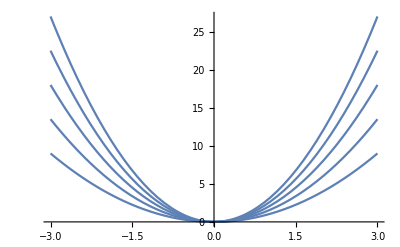

```mathematica
g[x_,y_,γ_]:=γ x^2+y
Plot3D[Table[g[x,γ],{γ,1,3,.5}],{x,-3,3},Plot]
```

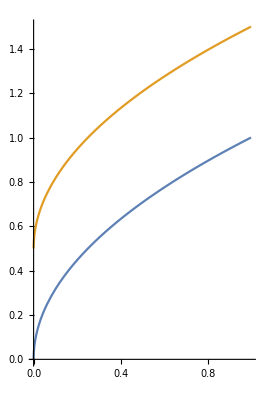

```mathematica
ParametricPlot[{{t,t^(1/2)},{t,t^(1/2)+.5}},{t,0,1}]
```

```mathematica
Eq1 = m D[x[t],{t,2}] == m D[y[t],{t,1}]D[ψ[t],{t,1}] + Subscript[F, x1] +Subscript[F, x2] +Subscript[F, x3] +Subscript[F, x4]/.rules
```

2050. x''[t]==-2 (Piecewise[{{80000. Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]+(26562.3 Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]^3)/(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)^2-(79843.3 Abs[Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]])/(√(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)), Abs[-0.11+0.1 e_y[t]+1.1 (ψ[t]-e_ψ[t])+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]<ArcTan[1.00196 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {-26719. Sign[-0.11+0.1 e_y[t]+1.1 (ψ[t]-e_ψ[t])+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]] √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2), Abs[-0.11+0.1 e_y[t]+1.1 (ψ[t]-e_ψ[t])+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]≥ArcTan[1.00196 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {0, True}}]) Sin[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]]+42590. (-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))+53438. Cos[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]] (-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))+2050. y'[t] ψ'[t]

```mathematica
Eq2 = m D[y[t],{t,2}] == -m D[x[t],{t,1}] D[ψ[t],{t,1}] + Subscript[F, y1]+ Subscript[F, y2]+ Subscript[F, y3]+ Subscript[F, y4]/.rules
```

2050. y''[t]==0.+2 (Piecewise[{{-80000. Tan[(y'[t]+1.43 ψ'[t])/x'[t]]-(41816.8 Tan[(y'[t]+1.43 ψ'[t])/x'[t]]^3)/(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)^2+(100180. Abs[Tan[(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[(y'[t]+1.43 ψ'[t])/x'[t]])/(√(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)), Abs[(y'[t]+1.43 ψ'[t])/x'[t]]<ArcTan[0.798563 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {-1/Sign[x'[t]]21295. Sign[y'[t]+1.43 ψ'[t]] √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2), Abs[(y'[t]+1.43 ψ'[t])/x'[t]]≥ArcTan[0.798563 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {0, True}}])+2 Cos[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]] (Piecewise[{{80000. Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]+(26562.3 Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]^3)/(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)^2-(79843.3 Abs[Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]])/(√(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)), Abs[-0.11+0.1 e_y[t]+1.1 (ψ[t]-e_ψ[t])+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]<ArcTan[1.00196 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {-26719. Sign[-0.11+0.1 e_y[t]+1.1 (ψ[t]-e_ψ[t])+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]] √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2), Abs[-0.11+0.1 e_y[t]+1.1 (ψ[t]-e_ψ[t])+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]≥ArcTan[1.00196 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {0, True}}])+53438. Sin[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]] (-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))-2050. x'[t] ψ'[t]

```mathematica
Eq3 =Subscript[J, z] D[ψ[t],{t,2}] == Subscript[l, f](Subscript[F, y1] + Subscript[F, y2]) - Subscript[l, r]*(Subscript[F, y3] + Subscript[F, y4]) + (Subscript[ω, t]/2)(-Subscript[F, x1] + Subscript[F, x2] - Subscript[F, x3] + Subscript[F, x4])/.rules
```

3344. ψ''[t]==0.-1.47 (0.+2 (Piecewise[{{-80000. Tan[(y'[t]+1.43 ψ'[t])/x'[t]]-(41816.8 Tan[(y'[t]+1.43 ψ'[t])/x'[t]]^3)/(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)^2+(100180. Abs[Tan[(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[(y'[t]+1.43 ψ'[t])/x'[t]])/(√(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)), Abs[(y'[t]+1.43 ψ'[t])/x'[t]]<ArcTan[0.798563 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {-1/Sign[x'[t]]21295. Sign[y'[t]+1.43 ψ'[t]] √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2), Abs[(y'[t]+1.43 ψ'[t])/x'[t]]≥ArcTan[0.798563 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {0, True}}]))+1.43 (2 Cos[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]] (Piecewise[{{80000. Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]+(26562.3 Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]^3)/(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)^2-(79843.3 Abs[Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]-(y'[t]+1.43 ψ'[t])/x'[t]])/(√(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)), Abs[-0.11+0.1 e_y[t]+1.1 (ψ[t]-e_ψ[t])+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]<ArcTan[1.00196 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {-26719. Sign[-0.11+0.1 e_y[t]+1.1 (ψ[t]-e_ψ[t])+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]] √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2), Abs[-0.11+0.1 e_y[t]+1.1 (ψ[t]-e_ψ[t])+1.1 e_ψ[t]+(y'[t]+1.43 ψ'[t])/x'[t]]≥ArcTan[1.00196 √(1.-(-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t])))^2)]}, {0, True}}])+53438. Sin[0.11-0.1 e_y[t]-1.1 (ψ[t]-e_ψ[t])-1.1 e_ψ[t]] (-0.1 (1/2 (-1-Tanh[20 (-35+t)])+1/2 (1+Tanh[20 (-30+t)]))-0.5 (1/2 (-1-Tanh[20 (-25+t)])+1/2 (1+Tanh[20 (-20+t)]))+0.5 (1/2 (-1-Tanh[20 (-15+t)])+1/2 (1+Tanh[20 (-10+t)]))+0.1 (1/2 (-1-Tanh[20 (-5+t)])+1/2 (1+Tanh[20 t]))))

```mathematica
Eq4 = m D[Subscript[e, ψ][t],{t,1}]==m D[ψ[t],{t,1}]-m D[Subscript[ψ, d][t],{t,1}]/.variableRules2/.rules
```

2050. e_ψ'[t]==2050. ψ'[t]-2050. (ψ'[t]-e_ψ'[t])

```mathematica
Eq5 = m D[Subscript[e, y][t],{t,1}]==m D[y[t],{t,1}] Cos[Subscript[e, ψ][t]] + m D[x[t],{t,1}]Sin[Subscript[e, ψ][t]]/.rules//Simplify
```

1. Sin[e_ψ[t]] x'[t]+1. Cos[e_ψ[t]] y'[t]==1. e_y'[t]